```mathematica
AoA=Table[n,{n,-0.3,0.3,0.1}];
```

```mathematica
DecimalForm[AoA,{1,2}]
```

{-0.30,-0.20,-0.10,0.00,0.10,0.20,0.30}

```mathematica
points=ToExpression[Import["/home/tatjam/code/tfg/workdir/geom.dat","String"]];
```

```mathematica
Graphics3D[Polygon[points]]
```

-Graphics3D-

```mathematica
params=Map[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/params_" <> ToString[DecimalForm[#,{1,2}]] <> "_.dat"]&,AoA];
```

```mathematica
liftOverCamber=Map[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/spanwise_sol_" <> ToString[DecimalForm[#,{1,2}]] <> "_.dat"][[1]]&,AoA];
```

```mathematica
clOverCamberPrandtl=Map[Import["/home/tatjam/code/tfg/workdir/steady_rectangle/prandtl_" <> ToString[DecimalForm[#,{1,2}]] <> "_.dat"][[1]]&,AoA];
```

#### Lifting line theory

#### Comparison

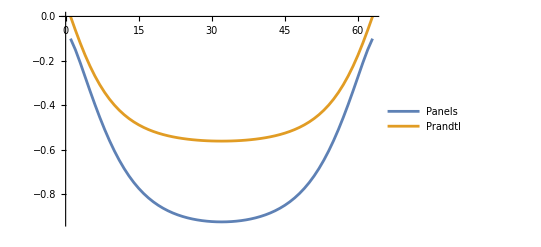

```mathematica
ListLinePlot[{liftOverCamber[[3]],clOverCamberPrandtl[[3]]},PlotLegends->{"Panels", "Prandtl"}]
```